# Mutual Information

```mathematica
SetDirectory[NotebookDirectory[]];
cd=ColorData[97,"ColorList"];
dir ="../AnalysisData/best_categ_pass_agent/";
(*dir = "../AnalysisData/best_offset/";*)
```

## By Subtasks

### Over time

```mathematica
aaO=Import[StringJoin[dir,"mi_size_inT_A_avoid.dat"]];
acO=Import[StringJoin[dir,"mi_size_inT_A_pass.dat"]];
baO=Import[StringJoin[dir,"mi_size_inT_B_avoid.dat"]];
bcO=Import[StringJoin[dir,"mi_size_inT_B_catch.dat"]];
```

```mathematica
max=3.5;
```

"The instantaneous co-fluctuation magnitude between pairs of brain regions.. 
The instantaneous task-relevant information co-fluctuation magnitude between pairs of brain regions..

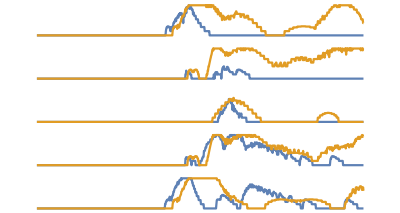

```mathematica
GraphicsColumn[
{
ListLinePlot[{baO[[1]],bcO[[1]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[2]],bcO[[2]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[3]],bcO[[3]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[4]],bcO[[4]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{baO[[5]],bcO[[5]]},PlotStyle->{cd[[1]],cd[[2]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
Export["MI_B_subtask_time.eps",%];
```

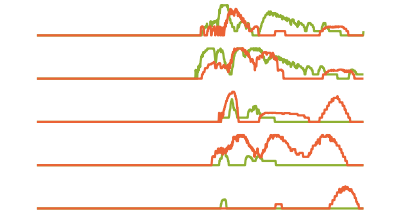

```mathematica
GraphicsColumn[
{
ListLinePlot[{aaO[[1]],acO[[1]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[2]],acO[[2]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[3]],acO[[3]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[4]],acO[[4]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[{aaO[[5]],acO[[5]]},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
Export["MI_A_subtask_time.eps",%];
```

### Time-averaged

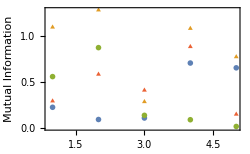

SubtaskMIe.eps

```mathematica
aa={Mean[aaO[[1]]],Mean[aaO[[2]]],Mean[aaO[[3]]],Mean[aaO[[4]]],Mean[aaO[[5]]]};
ac={Mean[acO[[1]]],Mean[acO[[2]]],Mean[acO[[3]]],Mean[acO[[4]]],Mean[acO[[5]]]};
ba={Mean[baO[[1]]],Mean[baO[[2]]],Mean[baO[[3]]],Mean[baO[[4]]],Mean[baO[[5]]]};
bc={Mean[bcO[[1]]],Mean[bcO[[2]]],Mean[bcO[[3]]],Mean[bcO[[4]]],Mean[bcO[[5]]]};
ListPlot[{ba,bc,aa,ac},PlotMarkers->{●,▲},PlotRange->All,Frame->True,ImageSize->250,FrameLabel->{"Neuron","Mutual Information"}]
Export["SubtaskMIe.eps",%]
```

### Time-averaged

```mathematica
aa=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_avoid.dat"]]];
ac=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_pass.dat"]]];
ba=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_avoid.dat"]]];
bc=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_catch.dat"]]];
```

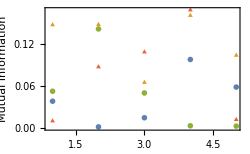

SubtaskMIe.eps

```mathematica
ListPlot[{ba,bc,aa,ac},PlotMarkers->{●,▲},PlotRange->All,Frame->True,ImageSize->250,FrameLabel->{"Neuron","Mutual Information"}]
Export["SubtaskMIe.eps",%]
```

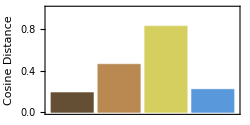

SubtaskCosMI.eps

```mathematica
BarChart[{CosineDistance[ba,bc],CosineDistance[aa,ac],CosineDistance[ba,aa],CosineDistance[bc,ac]},ChartStyle->"SouthwestColors",FrameLabel->{"","Cosine Distance"},AspectRatio->1/2,ChartStyle->{Black,Gray},PlotRange->{{0.5,4.5},{0.0,1.0}},Frame->True,ImageSize->250]
Export["SubtaskCosMI.eps",%]
```

## By Tasks

### Over time

```mathematica
aO=Import[StringJoin[dir,"mi_size_inT_A_both.dat"]];
bO=Import[StringJoin[dir,"mi_size_inT_B_both.dat"]];
```

```mathematica
max=4.5;
```

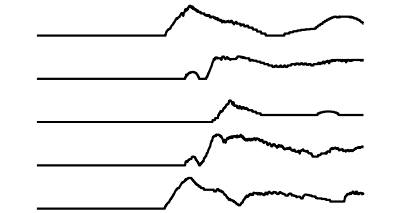

```mathematica
GraphicsColumn[
{
ListLinePlot[bO[[1]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[bO[[2]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[bO[[3]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[bO[[4]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[bO[[5]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
Export["MI_B_time.eps",%];
```

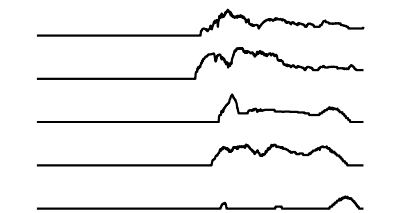

```mathematica
GraphicsColumn[
{
ListLinePlot[aO[[1]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aO[[2]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aO[[3]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aO[[4]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aO[[5]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
Export["MI_A_time.eps",%];
```

### Time-averaged

```mathematica
aT=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_both.dat"]]];
bT=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_both.dat"]]];
```

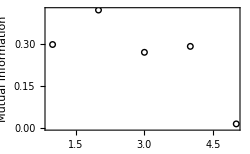

```mathematica
ListPlot[aT,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{○}]
Export["MI_A.eps",%];
```

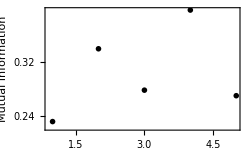

```mathematica
ListPlot[bT,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
Export["MI_B.eps",%];
```

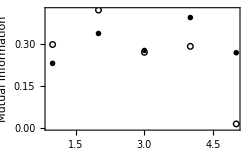

```mathematica
ListPlot[{aT,bT},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{○,●}]
Export["MI_AB.eps",%];
```

## All data

### Over time

```mathematica
cO=Import[StringJoin[dir,"mi_size_inT_both_both.dat"]];
```

### Time-averaged

```mathematica
cT=Flatten[Import[StringJoin[dir,"mi_size_tavg_both_both.dat"]]];
```

```mathematica
ListPlot[mi1,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
```

ListPlot::lpn: mi1 is not a list of numbers or pairs of numbers.

ListPlot[mi1,PlotRange→All,Frame→True,FrameLabel→{Neuron,Mutual Information},ImageSize→250,PlotStyle→GrayLevel[0],PlotMarkers→{●}]